## 7 Optimal Execution with Continuous Trading II

## 7.2 Optimal Acquisition with a Price Limiter

```mathematica
Clear["Global`*"]
```

## 7.3 Incorporating Order Flow

#### Simulation params

```mathematica
Clear["Global`*"]
T = 1;
k = 10^-3;(*Temp Impact*)
b = 10^-4;(*Perm Impact*)
λ=1000;(*the intensity of order flow process*)
η0=5;    (*orderflow jumps*)
κ=10;   (*orderflow decay speed*)

ϕ=10^-2;(*penalty*)
α=100; (*penalty*)
σ=10^-1;
γ=√(ϕ/k);

ζ=N@((α-1/2 b+√(k*ϕ))/(α-1/2 b-√(k*ϕ)));
```

The price dynamics is given by 
	
	ⅆ S_t=σⅆ W_t+b(μ_t-𝓋_t)ⅆt

From (7.6), the baseline strategy (Almgren-Chriss) is given by

```mathematica
vAC[t_]:=√(k ϕ)((α+√(k ϕ))/(α-√(k ϕ))*ⅇ^(2*γ*(T-t))+1)/((α+√(k ϕ))/(α-√(k ϕ))*ⅇ^(2*γ*(T-t))-1)
```

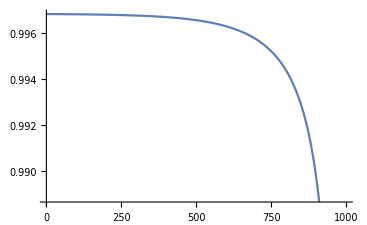

```mathematica
ListLinePlot@Table[1-vAC[t],{t,Range[0,T,0.001]}]
```

And the proposed strategy is expressed as

```mathematica
χ[t_]:=√(k*ϕ)*(1+ζ*ⅇ^(2*γ*(T-t)))/(1-ζ*ⅇ^(2*γ*(T-t)));
l1bar[τ_]:=1/(ζ ⅇ^(γ τ)-ⅇ^(-γ τ))(ⅇ^(γ τ)*(1-ⅇ^(-(κ+γ)*τ))/(κ+γ)*ζ-ⅇ^(-γ τ)*(1-ⅇ^(-(κ-γ)*τ))/(κ-γ));
v[t_,qt_,μt_]:=-1/k χ[t]qt-b/(2 k)*l1bar[t]*μt;
```

```mathematica
simNum=10;
steps = 3000;
dt=T/steps//N;
timeLine = Range[0,T,dt];
```

Following the notation in the book

```mathematica
μ=ConstantArray[0,{simNum,steps+1}];(*Order Flow*)


S=ConstantArray[0,{simNum,steps+1}];(*Execution Price*)
S⟦All,1⟧=50;(*initial price*)
Q=ConstantArray[0,{simNum,steps+1}]; (*Inventory*)
Q⟦All,1⟧=1;(*starting inventory*)
X=ConstantArray[0,{simNum,steps+1}] ;(*Trading Cost*)
ν=ConstantArray[0,{simNum,steps+1}] ;(**Trading Speed*)


acX=ConstantArray[0,{simNum,steps+1}] ;(*Baseline's Trading Cost*)
acQ=ConstantArray[0,{simNum,steps+1}]; (*Baseline's Inventory*)
acQ⟦All,1⟧=1;
acS = ConstantArray[0,{simNum,steps+1}]; (*Baseline's Execution Price*)
acS⟦All,1⟧=50;
acν=ConstantArray[0,{simNum,steps+1}] ;(*Basline's Trading Speed*)
```

```mathematica
Do[
ν⟦All,i⟧=v[timeLine⟦i⟧,Q⟦All,i⟧,μ⟦All,i⟧];
acν⟦All,i⟧=,

{i,Length@timeLine}]
```

{99999.9,200000.,300000.}

```mathematica
v[timeLine⟦1⟧,Q⟦All,1⟧,μ⟦All,1⟧]
```

{3.17363,3.17363,3.17363,3.17363,3.17363,3.17363,3.17363,3.17363,3.17363,3.17363}